```mathematica
{Needs["SpinChain`"],Needs["Carlos`"],Needs["Quantum`"]};
```

## GSE

### Check that the routine “RandomGSEDeltaOne” spits eigenvalues between +- Sqrt[8 * nsize]

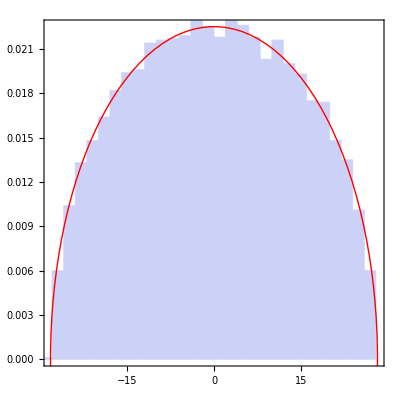

```mathematica
dim=100;EnsembleSize=100;
x=Table[ReadListUncomment["!./test_rmt -o get_gse_spectrum -s 0 -n "<>ToString[dim]][[1;;-1;;2]],{EnsembleSize}];
Show[{Histogram[Flatten[x],Automatic,"PDF"],Graphics[{Hue[0],Circle[{0,0},{Sqrt[8dim],2/(π Sqrt[8dim])}]}]},AspectRatio->1,Frame->True,PlotRange->{{-Sqrt[8dim],Sqrt[8dim]},{0,2/(π Sqrt[8dim])}},PlotRangePadding->None,PlotRangeClipping->True]
```

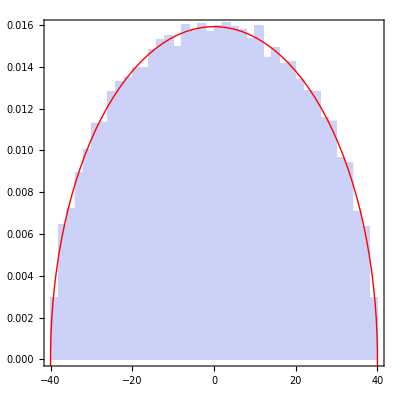

```mathematica
dim=200;EnsembleSize=100;
x=Table[ReadListUncomment["!./test_rmt -o get_gse_spectrum -s 0 -n "<>ToString[dim]][[1;;-1;;2]],{EnsembleSize}];
Show[{Histogram[Flatten[x],Automatic,"PDF"],Graphics[{Hue[0],Circle[{0,0},{Sqrt[8dim],2/(π Sqrt[8dim])}]}]},AspectRatio->1,Frame->True,PlotRange->{{-Sqrt[8dim],Sqrt[8dim]},{0,2/(π Sqrt[8dim])}},PlotRangePadding->None,PlotRangeClipping->True]
```

### Check that the unfolded GSE is flat

```mathematica
DistributionFunction[x_,dim_]:=If[Abs[x]>dim/2,0,1/dim]
```

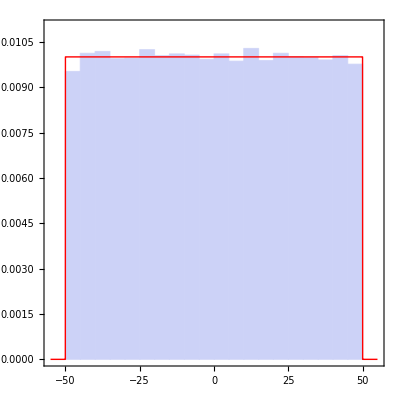

```mathematica
dim=100;EnsembleSize=200;
x=Table[ReadListUncomment["!./test_rmt -o get_gse_flat_spectrum -s 0 -n "<>ToString[dim]][[1;;-1;;2]],{EnsembleSize}];
Show[{Histogram[Flatten[x],Automatic,"PDF"],Plot[DistributionFunction[x,dim],{x,-1.1dim/2,1.1dim/2},PlotStyle->Hue[0]]},AspectRatio->1,Frame->True,PlotRange->{{-1.1dim/2,1.1dim/2},{0,1.1/dim}},PlotRangePadding->None,PlotRangeClipping->True]
```

### Check that the unfolded GSE P(s) and K2(s)

```mathematica
x=Flatten[Table[Drop[RotateLeft[#]-#&[ReadListUncomment["!./test_rmt -o get_gse_flat_spectrum -s 0 -n "<>ToString[dim]][[1;;-1;;2]]],-1],{EnsembleSize}]];
```

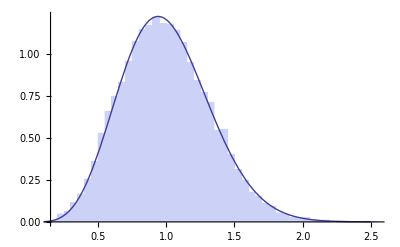

```mathematica
Show[{Histogram[x/2,Automatic,"PDF"],Plot[P[s,4],{s,0,2.5}]}]
```

```mathematica
tmax=5;
Npoints=200;
dim=100;EnsembleSize=200;
y=Mean[Table[
x=ReadListUncomment["!./test_rmt -o get_gse_flat_spectrum -s 0 -n "<>ToString[dim]][[1;;-1;;2]];
Table[Abs[Total[Exp[-ⅈ x t]]]^2/(dim/2),{t,0,tmax,tmax/Npoints}]
,{EnsembleSize}]];
```

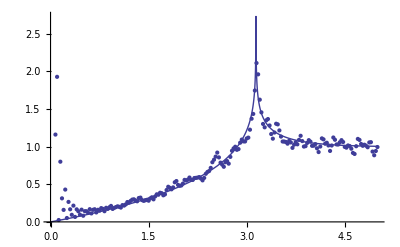

```mathematica
Show[{Plot[K2[s/π,4],{s,0,5}],ListPlot[y,DataRange->{0,tmax}]}]
```

## Test that the building blocks of the Ising Chain are correct

### Test that the building blocks of the Ising Chain are correct

```mathematica
{q=10,Targets=RandomSample[Range[0,q-1],2],J=Random[]};
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@(ψ=RandomState[Power[2,q]])];
Chop[ψoutc=#[[1]]+ⅈ#[[2]]&/@ReadList["!./test_spins -o test_ising_single -q "<>ToString[q]<>" --ising_z "<>ToString[J,InputForm,NumberMarks->False]<>" --position "<>ToString[Targets[[1]]]<>" --position2 "<>ToString[Targets[[2]]],Number,RecordLists->True]];
Norm[ψoutc-ApplyIsing[ψ,J,Targets[[1]],Targets[[2]]]]
```

1.32353×10^-16

```mathematica
{q=12,b=Table[Random[]-.5,{3}]};
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@(ψ=RandomState[Power[2,q]])];
tc=AbsoluteTiming[ψoutc=#[[1]]+ⅈ#[[2]]&/@ReadList["!./test_spins -o test_kick -q "<>ToString[q]<>" --bx "<>ToString[b[[1]],InputForm,NumberMarks->False]<>" --by "<>ToString[b[[2]],InputForm,NumberMarks->False]<>" --bz "<>ToString[b[[3]],InputForm,NumberMarks->False],Number,RecordLists->True];];
tm=AbsoluteTiming[ψoutMathematica=ApplyMagnetickKick[ψ,b];];
{tc[[1]],tm[[1]],Norm[ψoutc-ψoutMathematica]}
```

{0.12765,4.542282,9.90078×10^-16}

```mathematica
q=5;QubitToAdress=Random[Integer,{0,q-1}];
ψ=RandomState[Power[2,q]];
b={N[π,16],0.1,0.};
b=Table[Random[]-.5,{3}];
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@ψ];
tc=AbsoluteTiming[ψoutc=#[[1]]+ⅈ#[[2]]&/@ReadList["!./test_spins -o test_kick_single_spin -q "<>ToString[q]<>" --position "<>ToString[QubitToAdress]<>" --bx "<>ToString[b[[1]],InputForm,NumberMarks->False]<>" --by "<>ToString[b[[2]],InputForm,NumberMarks->False]<>" --bz "<>ToString[b[[3]],InputForm,NumberMarks->False],Number,RecordLists->True];];
tm=AbsoluteTiming[ψoutMathematica=ApplyMagnetickKick[ψ,b,QubitToAdress];];
{tc[[1]],tm[[1]],Norm[ψoutc-ψoutMathematica]}
```

{0.005602,0.00289,2.36235×10^-16}

### Test that the topologies Ising Chain are correct

```mathematica
{QubitsEnvironment=10,Jcoupling=0.01Random[],Jenvironment=Random[],b=Table[Random[],{3}]};
state=RandomState[Power[2,2+QubitsEnvironment]];
StateAfterMathematicaRoutine=ApplyCommonEnvironment[state,b,Jenvironment,Jcoupling];
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@state];
Chop[ψoutc=#[[1]]+ⅈ#[[2]]&/@ReadList["!./test_spins -o test_apply_common_environment_chain -q "<>ToString[QubitsEnvironment+2]<>" --ising_z "<>ToString[Jenvironment,InputForm,NumberMarks->False]<>" --coupling "<>ToString[Jcoupling,InputForm,NumberMarks->False]<>" --bx "<>ToString[b[[1]],InputForm,NumberMarks->False]<>" --by "<>ToString[b[[2]],InputForm,NumberMarks->False]<>" --bz "<>ToString[b[[3]],InputForm,NumberMarks->False],Number,RecordLists->True]];
Norm[ψoutc-StateAfterMathematicaRoutine]
```

1.19316×10^-15

### Test that the topologies DephasingChane is correct

```mathematica
Get["SpinChain`"];
{QubitsEnvironment=4,JcouplingQubitRing=Random[],Jenvironment=Random[],benv=Table[Random[],{3}],Delta=Random[]};
state=tensorProduct[RandomState[Power[2,QubitsEnvironment]],RandomState[2]];
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@state];
StateAfterMathematicaRoutine=ApplyDephasingChain[state,Delta,Jenvironment,benv,JcouplingQubitRing];
Chop[ψoutc=#[[1]]+ⅈ#[[2]]&/@ReadList[a="!./test_spins -o test_dephasing_chain -q "<>ToString[QubitsEnvironment+1]<>" --ising_z "<>ToString[Jenvironment,InputForm,NumberMarks->False]<>" --coupling "<>ToString[JcouplingQubitRing,InputForm,NumberMarks->False]<>" --bx "<>ToString[benv[[1]],InputForm,NumberMarks->False]<>" --by "<>ToString[benv[[2]],InputForm,NumberMarks->False]<>" --bz "<>ToString[benv[[3]],InputForm,NumberMarks->False]<>" --Delta "<>ToString[Delta],Number,RecordLists->True]];
Norm[ψoutc-StateAfterMathematicaRoutine]
```

8.92198×10^-8

```mathematica
Get["SpinChain`"];
{QubitsEnvironment=4,JcouplingQubitRing=Random[],Jenvironment=Random[],benv=Table[Random[],{3}],Delta=Random[]};
state=tensorProduct[RandomState[Power[2,QubitsEnvironment]],RandomState[2]];
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@state];
StateAfterMathematicaRoutine=ApplyDephasingChain[state,Delta,Jenvironment,benv,JcouplingQubitRing];
Chop[ψoutc=#[[1]]+ⅈ#[[2]]&/@ReadList[a="!./test_spins -o test_dephasing_chain -q "<>ToString[QubitsEnvironment+1]<>" --ising_z "<>ToString[Jenvironment,InputForm,NumberMarks->False]<>" --coupling "<>ToString[JcouplingQubitRing,InputForm,NumberMarks->False]<>" --bx "<>ToString[benv[[1]],InputForm,NumberMarks->False]<>" --by "<>ToString[benv[[2]],InputForm,NumberMarks->False]<>" --bz "<>ToString[benv[[3]],InputForm,NumberMarks->False]<>" --Delta "<>ToString[Delta,InputForm,NumberMarks->False],Number,RecordLists->True]];
Norm[ψoutc-StateAfterMathematicaRoutine]
```

4.95073×10^-16

## Test bitwise operations

### Testing routine insert_bit

```mathematica
GetNumberFromProgram[NumberToManipulate_,TargetBit_,Bit_]:=ReadListUncomment["!./testing  -o test_insert_bit --i1 "<>ToString[NumberToManipulate]<>" --i2 "<>ToString[TargetBit]<>" --i3 "<>ToString[Bit],Number][[1]]
```

```mathematica
TargetBitMax=5;
NumberToManipulateMax=80;
ResultsMathematica=Table[{NumberToManipulate,MergeTwoIntegers[0,NumberToManipulate,Power[2,TargetBit]],MergeTwoIntegers[1,NumberToManipulate,Power[2,TargetBit]]},{NumberToManipulate,0,NumberToManipulateMax},{TargetBit,0,TargetBitMax}];
Resultscpp=Table[{NumberToManipulate,GetNumberFromProgram[NumberToManipulate,TargetBit,0],GetNumberFromProgram[NumberToManipulate,TargetBit,1]},{NumberToManipulate,0,NumberToManipulateMax},{TargetBit,0,TargetBitMax}];
```

```mathematica
Norm[Flatten[ResultsMathematica-Resultscpp]]
```

0

### Testing rotate bits

```mathematica
RotateBitsMathematica[NumberIn_,NumberOfQubits_]:=FromDigits[RotateRight[IntegerDigits[NumberIn,2,NumberOfQubits]],2]
RotateBitsCpp[NumberIn_,NumberOfQubits_]:=ReadListUncomment["!./testing  -o test_rotate_bits --i1 "<>ToString[NumberIn]<>" --i2 "<>ToString[NumberOfQubits],Number][[1]]
```

```mathematica
NumberOfQubits=8;
Norm[Table[RotateBitsMathematica[NumberIn,NumberOfQubits]-RotateBitsCpp[NumberIn,NumberOfQubits],{NumberIn,0,Power[2,NumberOfQubits]-1}]]
```

0

```mathematica
AllBitRotationsMathematica[NumberIn_,NumberOfQubits_]:=Sort[Union[NestList[RotateBitsMathematica[#,NumberOfQubits]&,NumberIn,NumberOfQubits-1]]]
```

```mathematica
AllBitRotationsCpp[NumberIn_,NumberOfQubits_]:=ReadListUncomment["!./testing  -o test_all_bit_rotations --i1 "<>ToString[NumberIn]<>" --i2 "<>ToString[NumberOfQubits],Number]
```

```mathematica
NumberOfQubits=7;
Norm[Table[Norm[Sort[AllBitRotationsCpp[NumberIn,NumberOfQubits]]-AllBitRotationsMathematica[NumberIn,NumberOfQubits]],{NumberIn,0,Power[2,NumberOfQubits]-1}]]
```

0

```mathematica
ReverseBitsMathematica[NumberIn_,NumberOfQubits_]:=FromDigits[Reverse[IntegerDigits[NumberIn,2,NumberOfQubits]],2]
```

```mathematica
ReverseBitsCpp[NumberIn_,NumberOfQubits_]:=ReadListUncomment["!./testing  -o test_reverse_bits --i1 "<>ToString[NumberIn]<>" --i2 "<>ToString[NumberOfQubits],Number][[1]]
```

```mathematica
NumberOfQubits=8;
Norm[Table[ReverseBitsMathematica[NumberIn,NumberOfQubits]-ReverseBitsCpp[NumberIn,NumberOfQubits],{NumberIn,0,Power[2,NumberOfQubits]-1}]]
```

0

## Test σ creation operations

### extend_qubit _operator and sigma (sigma_array)

```mathematica
Norm[Table[ReadListUncomment["!./testing  -o  test_extend_qubit_operator_coherent_with_sigma --i1 "<>ToString[NumberOfQubits],Number][[1]],{NumberOfQubits,6}]]
```

0

## Test partial trace

```mathematica
Qubits=8;
Mask=1;

ψAB=RandomState[2^Qubits];
Export["/tmp/psiab.dat",{Re[#],Im[#]}&/@ψAB];
Norm[Table[ρ=Partition[#[[1]]+ⅈ #[[2]]&/@ReadListUncomment["!cat  /tmp/psiab.dat | ./testing -o test_partial_trace --i1 "<>ToString[Qubits]<>" --i2 "<>ToString[Mask],Number,RecordLists->True],Power[2,BitsOn[Mask]]];
ρA=Chop[PartialTrace[ψAB,Mask]];
Norm[ρ-ρA],{Mask,0,Power[2,Qubits-1]}]]
```

9.47883×10^-17

### Partial Trace for matrices

```mathematica
TotalQubits=2;
ρ=RandomDensityMatrix[Power[2,TotalQubits]];
Export["/tmp/rho.dat",{Re[#],Im[#]}&/@(Flatten[ρ])];
```

```mathematica
Mask=1;
Table[
ρAmath=PartialTrace[ρ,Mask];
ρAcpp=Partition[#[[1]]+ⅈ #[[2]]&/@ReadListUncomment["!cat  /tmp/rho.dat | ./testing -o test_partial_trace_mixed --i1 "<>ToString[TotalQubits]<>" --i2 "<>ToString[Mask],Number,RecordLists->True],Power[2,BitsOn[Mask]]];
Norm[ρAmath-ρAcpp],{Mask,0,Power[2,TotalQubits]-1}]
```

Part::partw: Part 3 of {0.594533, 0.0941415  - 0.0639532\ ⅈ}
 does not exist.

Part::partw: Part 3 of {{0.594533, 0.0941415  - 0.0639532\ ⅈ}, {0.0941415  + 0.0639532\ ⅈ, 0.405467}}
 does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{1.11022×10^-16,0.,Max[0.707107 √((0.271972+0. ⅈ)+(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧]+(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]-0.497373 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧]+(0.0792591-0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0792591+0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-0.497373 {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-√(((-0.271972+0. ⅈ)-(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧]-(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]+0.497373 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧]-(0.0792591-0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧-1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧-(0.0792591+0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+0.497373 {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧)^2-4. ((0.00289275+0. ⅈ)+(0.0042629+0.00227603 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧]+(0.0042629-0.00227603 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]+(0.0537843+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]-(0.00494309-1.40819×10^-19 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧]+(0.0042629-0.00227603 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0080728+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.00449121-0.00670814 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧-(0.00728438-0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0042629+0.00227603 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.00449121+0.00670814 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0080728+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-(0.00728438+0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0537843+0. ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-0.0919059 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-(0.00494309+1.40819×10^-19 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-(0.00728438+0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-(0.00728438-0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-0.0919059 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧+(0.00844669+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧))),0.707107 √((0.271972+0. ⅈ)+(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧]+(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]-0.497373 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧]+(0.0792591-0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0792591+0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-0.497373 {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧+√(((-0.271972+0. ⅈ)-(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧]-(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]+0.497373 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧]-(0.0792591-0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧-1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧-(0.0792591+0.0423178 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+0.497373 {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧)^2-4. ((0.00289275+0. ⅈ)+(0.0042629+0.00227603 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧]+(0.0042629-0.00227603 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]+(0.0537843+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧]-(0.00494309-1.40819×10^-19 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧]+(0.0042629-0.00227603 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0080728+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.00449121-0.00670814 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧-(0.00728438-0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧+(0.0042629+0.00227603 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.00449121+0.00670814 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0080728+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-(0.00728438+0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0537843+0. ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0792591+0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+(0.0792591-0.0423178 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧+1. Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-0.0919059 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧ {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧-(0.00494309+1.40819×10^-19 ⅈ) {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-(0.00728438+0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-(0.00728438-0.00388926 ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧-0.0919059 Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦1,3⟧] Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,1⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧+(0.00844669+0. ⅈ) Conjugate[{{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧] {{0.594533,0.0941415-0.0639532 ⅈ},{0.0941415+0.0639532 ⅈ,0.405467}}⟦3,3⟧)))],0.435601}

```mathematica
PartialTrace2[Rho_?MatrixQ,DigitsToLeave_]:=Module[{ab1,ab2,na,nb,n},
n=BitXor[Length[Rho]-1,DigitsToLeave];
na=Power[2,BitsOn[n]];
nb=Length[Rho]/na;
Table[
Sum[
(*Print[a,b1,n,DigitsToLeave,{MergeTwoIntegers[b1-1,a-1,DigitsToLeave],MergeTwoIntegers[a-1,b1-1,n]},{MergeTwoIntegers[b2-1,a-1,DigitsToLeave],MergeTwoIntegers[a-1,b2-1,n]}];*)
MergeTwoIntegers[b1-1,a-1,DigitsToLeave];
ab1=MergeTwoIntegers[a-1,b1-1,n];
ab2=MergeTwoIntegers[a-1,b2-1,n];
Rho[[ab1+1,ab2+1]],{a,na}],
{b1,nb},{b2,nb}]]
PartialTrace2[ρ,2]
```

{{0.50389+0. ⅈ,-0.00456248+0.0246231 ⅈ},{-0.00456248-0.0246231 ⅈ,0.49611+0. ⅈ}}

```mathematica
PartialTrace3[Rho_?MatrixQ,DigitsToLeave_]:=Module[{ab1,ab2,na,nb},
nb=Power[2,BitsOn[DigitsToLeave]];
na=Length[Rho]/nb;
Table[
Sum[
(*Print[a,b1,n,DigitsToLeave,{MergeTwoIntegers[b1-1,a-1,DigitsToLeave],MergeTwoIntegers[a-1,b1-1,n]},{MergeTwoIntegers[b2-1,a-1,DigitsToLeave],MergeTwoIntegers[a-1,b2-1,n]}];*)
ab1=MergeTwoIntegers[b1-1,a-1,DigitsToLeave];
ab2=MergeTwoIntegers[b2-1,a-1,DigitsToLeave];
Rho[[ab1+1,ab2+1]],{a,na}],
{b1,nb},{b2,nb}]]
PartialTrace2[ρ,2]-PartialTrace3[ρ,2]
```

{{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
MergeTwoIntegers
```

## Test Hadamard

```mathematica
{Needs["Quantum`"]};
q=7;
psi=RandomState[Power[2,q]];
Export["/tmp/estado.dat",{Re[#],Im[#]}&/@psi];
Norm[Table[psiout=#[[1]]+ⅈ#[[2]]&/@ReadList["!cat /tmp/estado.dat | ./test_spins -o test_hadamard --qubits "<>ToString[q]<>" --position "<>ToString[TargetQubit],Number,RecordLists->True];
psioutMathematica=ApplyGate[Hadamard[],psi,TargetQubit];
Dot[Conjugate[psioutMathematica],psiout]-1,{TargetQubit,0,q-1}]]
```

1.60046×10^-16

## Test Sum σ_x

```mathematica
Directory[]
```

/home/carlosp/investigacion/libs/cpp

```mathematica
{q=7,dim=Power[2,q],ψ=RandomState[dim]};
Export["/tmp/psi.dat",{Re[#],Im[#]}&/@ψ];
ψcpp=#[[1]]+ⅈ#[[2]]&/@ReadListUncomment["!cat  /tmp/psi.dat | ./testing -o test_sum_sigma_x --i1 "<>ToString[q],Number,RecordLists->True];
Norm[SumSigmaX[q].ψ-ψcpp]
```

3.44338×10^-16

## Test GetState

### Pure Version

```mathematica
{DimA=2,DimB=2};
{dim=DimA DimB,ψAB=RandomState[dim],H=GUEMember[dim],t=Random[]};
Export["/tmp/psiab.dat",{Re[#],Im[#]}&/@(Flatten[{ψAB,Flatten[H]}])];
ψcpp=#[[1]]+ⅈ#[[2]]&/@ReadListUncomment["!cat  /tmp/psiab.dat | ./testing -o test_GetState --i1 "<>ToString[DimA]<>" --i2 "<>ToString[DimB]<>" --d1 "<>ToString[t,InputForm,NumberMarks->False],Number,RecordLists->True];
```

```mathematica
Norm[MatrixExp[-ⅈ t H].ψAB-ψcpp]
```

4.20934×10^-16

### Mixed Version

```mathematica
{DimA=2,DimB=2};
{dim=DimA DimB,ψAB=RandomState[dim],H=GUEMember[dim],t=Random[]};
Export["/tmp/psiab.dat",{Re[#],Im[#]}&/@(Flatten[{ψAB,Flatten[H]}])];
```

```mathematica
ρcpp=Partition[#[[1]]+ⅈ#[[2]]&/@ReadListUncomment["!cat  /tmp/psiab.dat | ./testing -o test_GetState_mixed --i1 "<>ToString[DimA]<>" --i2 "<>ToString[DimB]<>" --d1 "<>ToString[t,InputForm,NumberMarks->False],Number,RecordLists->True],DimA];
```

```mathematica
Norm[PartialTrace[MatrixExp[-ⅈ t H].ψAB,DimA-1]-ρcpp]
Chop[Purity[ρcpp]]
```

7.05935×10^-16

0.728788